```mathematica
SetDirectory["~/Dropbox/Supernova/stability/angles/figs"];
<<"CustomTicks.m"
```

```mathematica
ϵ=.
μ=.
Ω=.
u=.
i0=Integrate[(-μ/(-1+u ϵ μ-Ω)+(1+ϵ)μ/(1+u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
i1=Integrate[u(-μ/(-1+u ϵ μ-Ω)+(1+ϵ)μ/(1+u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
i2=Integrate[u^2(-μ/(-1+u ϵ μ-Ω)+(1+ϵ)μ/(1+u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
```

((1+ϵ) Log[1-(ϵ μ)/(-1+Ω)]-Log[1-(ϵ μ)/(1+Ω)])/ϵ

(ϵ^2 μ+2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+ϵ μ-Ω]+Log[1+Ω]-Log[1-ϵ μ+Ω]-Ω Log[1-ϵ μ+Ω])/(ϵ^2 μ)

1/(2 ϵ^3 μ^2)(-4 ϵ μ-2 ϵ^2 μ+ϵ^3 μ^2+2 ϵ^2 μ Ω-2 (1+ϵ) (-1+Ω)^2 Log[1-Ω]+2 (1+ϵ) (-1+Ω)^2 Log[1+ϵ μ-Ω]+2 Log[1+Ω]+4 Ω Log[1+Ω]+2 Ω^2 Log[1+Ω]-2 Log[1-ϵ μ+Ω]-4 Ω Log[1-ϵ μ+Ω]-2 Ω^2 Log[1-ϵ μ+Ω])

```mathematica
FullSimplify[(h+i1)^2-i0 i2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals]
```

(1+h+(2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+ϵ μ-Ω]+Log[1+Ω]-Log[1-ϵ μ+Ω]-Ω Log[1-ϵ μ+Ω])/(ϵ^2 μ))^2-1/(2 ϵ^4 μ^2)(ϵ μ (-4+ϵ (-2+ϵ μ+2 Ω))-2 (1+ϵ) (-1+Ω)^2 Log[1-Ω]+2 (1+ϵ) (-1+Ω)^2 Log[1+ϵ μ-Ω]+2 (1+Ω)^2 Log[1+Ω]-2 Log[1-ϵ μ+Ω]-2 Ω (2+Ω) Log[1-ϵ μ+Ω]) ((1+ϵ) Log[1-(ϵ μ)/(-1+Ω)]-Log[1-(ϵ μ)/(1+Ω)])

```mathematica
d[h_,ϵ_,μ_,Ω_]:=(1+h+1/(ϵ^2 μ)(2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+ϵ μ-Ω]+Log[1+Ω]-Log[1-ϵ μ+Ω]-Ω Log[1-ϵ μ+Ω]))^2-1/(2 ϵ^4 μ^2)(ϵ μ (-4+ϵ (-2+ϵ μ+2 Ω))-2 (1+ϵ) (-1+Ω)^2 Log[1-Ω]+2 (1+ϵ) (-1+Ω)^2 Log[1+ϵ μ-Ω]+2 (1+Ω)^2 Log[1+Ω]-2 Log[1-ϵ μ+Ω]-2 Ω (2+Ω) Log[1-ϵ μ+Ω]) ((1+ϵ) Log[1-(ϵ μ)/(-1+Ω)]-Log[1-(ϵ μ)/(1+Ω)])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

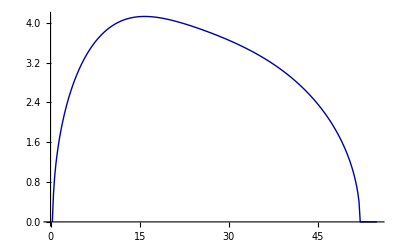

```mathematica
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[-1,0.5,m,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
t1=Table[{m,k[m]},{m,0.3,55.,0.2}];
f1=ListLinePlot[t1,PlotStyle->{Darker[Blue],Thick},PlotRange->{{0,55},All}]
```

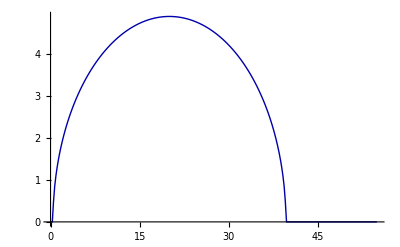

```mathematica
k2[μ_,ϵ_]:=Sqrt[(4-8μ-4 ϵ μ+(ϵ μ)^2)/4]
ϵ=1/2;
t2=Table[{m,Im[k2[m,ϵ]]},{m,0.1,55.,0.2}];
t4=Table[{m,Im[k4[m,ϵ]]},{m,0.1,37.,0.2}];
f2=ListLinePlot[{t2,t4},PlotStyle->{Darker[Blue],Thick},PlotRange->{{0,55},All}]
```

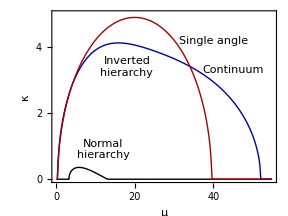

```mathematica
Show[plot1,
Graphics[Text["Inverted\nhierarchy",{18,3.4},BaseStyle->{12}]],
Graphics[Text["Continuum",{45,3.3},BaseStyle->{12,Darker[Blue]}]],
Graphics[Text["Single angle",{40,4.2},BaseStyle->{12,Darker[Red]}]],
Graphics[Text["Normal\nhierarchy",{12,0.9},BaseStyle->{12}]]
]
```

```mathematica
Export["single1.eps",%]
```

single1.eps

```mathematica
],Inset["Continuum",{45,3.3},{Center,Center}],Inset["Single Angle",{40,4.2},{Center,Center}]}
```

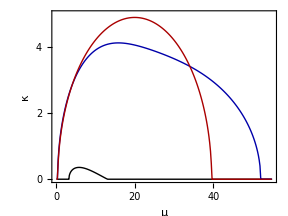

```mathematica
plot1=ListLinePlot[{t3,t1,t2},PlotRange->{{0,55},{0,5}},
ImageSize->4 72,AspectRatio->3/4,
PlotStyle->{{AbsoluteThickness[1],Black},{AbsoluteThickness[1],Darker[Blue]},{AbsoluteThickness[1],Darker[Red]}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,RotateLabel->False,
FrameStyle->AbsoluteThickness[1],FrameLabel->{Style["μ",14],Style["κ",14]},
FrameTicks->{LinTicks[0,60,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,60,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
```

```mathematica
ϵ=.
μ=.
Ω=.
u=.
i0=Integrate[(-μ/(-1+0u ϵ μ-Ω)+(1+ϵ)μ/(1+0u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
i1=Integrate[u(-μ/(-1+0u ϵ μ-Ω)+(1+ϵ)μ/(1+0u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
i2=Integrate[u^2(-μ/(-1+0u ϵ μ-Ω)+(1+ϵ)μ/(1+0u ϵ μ-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals]
```

-μ/(-1-Ω)+((1+ϵ) μ)/(1-Ω)

-(μ (2+ϵ+ϵ Ω))/(2 (-1+Ω^2))

-(μ (2+ϵ+ϵ Ω))/(3 (-1+Ω^2))

```mathematica
FullSimplify[(1+i1)^2-i0 i2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals]
```

-(μ^2 (2+ϵ+ϵ Ω)^2+12 μ (2+ϵ+ϵ Ω) (-1+Ω^2)-12 (-1+Ω^2)^2)/(12 (-1+Ω^2)^2)

```mathematica
ϵ=.
Solve[-(μ^2 (2+ϵ+ϵ Ω)^2+12 μ (2+ϵ+ϵ Ω) (-1+Ω^2)-12 (-1+Ω^2)^2)/(12 (-1+Ω^2)^2)==0,Ω]//FullSimplify
```

{{Ω→1/12 ((3-2 √3) ϵ μ-√(144+(72-48 √3) (2+ϵ) μ+3 (7-4 √3) ϵ^2 μ^2))},{Ω→1/12 ((3-2 √3) ϵ μ+√(144+(72-48 √3) (2+ϵ) μ+3 (7-4 √3) ϵ^2 μ^2))},{Ω→1/12 ((3+2 √3) ϵ μ-√3 √(48+8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2))},{Ω→1/12 ((3+2 √3) ϵ μ+√3 √(48+8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2))}}

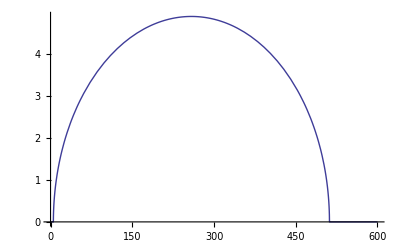

```mathematica
ϵ=1/2;
Plot[Im[1/12 ((3-2 √3) ϵ μ+√(144+(72-48 √3) (2+ϵ) μ+3 (7-4 √3) ϵ^2 μ^2))],{μ,0.,600}]
```

```mathematica
ϵ=0.5
Solve[48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2==0,μ]//FullSimplify
```

0.5

{{μ→0.37507},{μ→36.7531}}

```mathematica
12-8 √3//N
```

-1.85641

```mathematica
ϵ=.
μ=.
k=√3 √(48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2)/12//FullSimplify
```

(√(48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2))/(4 √3)

```mathematica
k4[μ_,ϵ_]:=(√(48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2))/(4 √3)
```

```mathematica
FullSimplify[k^2]
```

```mathematica
ϵ=1/2
Solve[1/48 (48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2)==0,μ]//FullSimplify
```

1/2

{{μ→8 (-15-12 √2+10 √3+6 √6)},{μ→-120+96 √2+80 √3-48 √6}}

```mathematica
D[1/48 (48-8 (3+2 √3) (2+ϵ) μ+(7+4 √3) ϵ^2 μ^2),μ]//FullSimplify
```

```mathematica
Solve[1/96 (-40 (3+2 √3)+(7+4 √3) μ)==0,μ]//FullSimplify
```

```mathematica
{{μ->40 (-3+2 √3)}}
```

{{μ→40 (-3+2 √3)}}

```mathematica
μ=40 (-3+2 √3)
k//FullSimplify
```

40 (-3+2 √3)

2 ⅈ √6

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

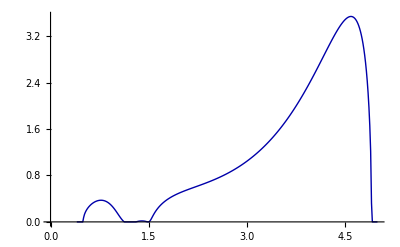

```mathematica
Clear[k]
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[1,0.5,m,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
s1=Table[{a,k[10^a]},{a,4.99,0.4,-0.013}];
ListLinePlot[s1,PlotStyle->{Darker[Blue],Thick}]
```

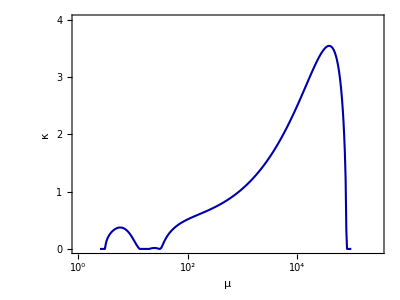

single2.eps

```mathematica
plot2=ListLinePlot[{s1},PlotRange->{{0,Log[10,300000]},{0,4}},
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},AspectRatio->3/4,
PlotStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[1.],Darker[Red]},{AbsoluteThickness[1.],Black}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["μ",14],Style["κ",14]},
FrameTicks->{LogTicks[0,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
Export["single2.eps",plot2]
```

```mathematica
Epilog-> {Inset["Continuum",{47,3.1},{Center,Center}],Inset["Single Angle",{40,4.1},{Center,Center}],Inset["λ = -ϵμ",{31,1.0},{Center,Center}]},
```